```mathematica
SetOptions[ListPlot,Joined->True,Frame->True,LabelStyle->{FontFamily->Times,FontSize->12,FontWeight->Bold}]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→True,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,Joined→True,LabelStyle→{FontFamily→Times,FontSize→12,FontWeight→Bold},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{}}

```mathematica
Luft=Import["00-Luft.DPT","Table"];
LuftNorm=Transpose[{Luft⟦All,1⟧,Luft⟦All,2⟧/Max[Luft⟦All,2⟧]}];
```

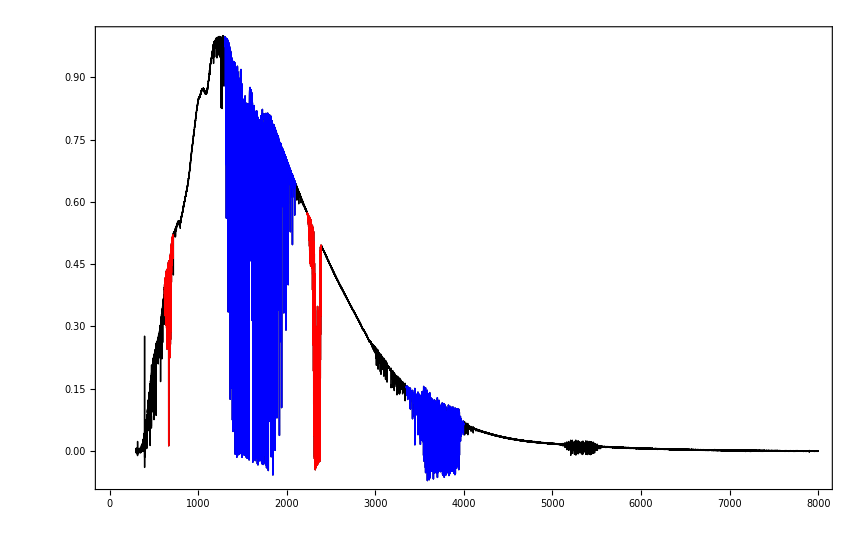

```mathematica
ListPlot[{Take[LuftNorm,{1,63875}],Take[LuftNorm,{46534,47859}],Take[LuftNorm,{60390,61220}],Take[LuftNorm,{33177,38574}],Take[LuftNorm,{48940,55578}]}, PlotStyle->{Black,Red,Red,Blue,Blue}]
```

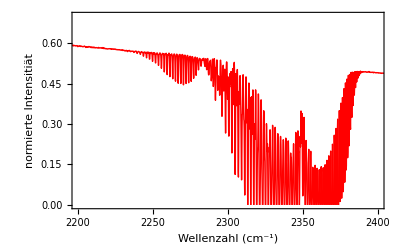

```mathematica
CO2a=ListPlot[LuftNorm,PlotRange->{{2200,2400},{0,0.7}},FrameLabel->{"Wellenzahl (cm^-1)","normierte Intensitiät"},PlotStyle->{Red}]
```

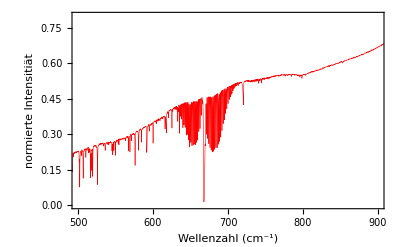

```mathematica
CO2b=MultipleListPlot[LuftNorm,PlotRange->{{500,900},{0,0.8}},FrameLabel->{"Wellenzahl (cm^-1)","normierte Intensitiät"},PlotStyle->{Red}]
```

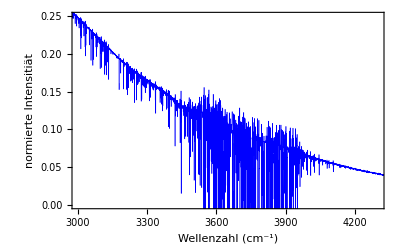

```mathematica
H2Oa=MultipleListPlot[LuftNorm,PlotRange->{{3000,4300},{0,0.25}},FrameLabel->{"Wellenzahl (cm^-1)","normierte Intensitiät"},PlotStyle->{Blue}]
```

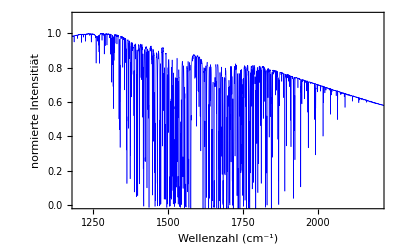

```mathematica
H2Ob=MultipleListPlot[LuftNorm,PlotRange->{{1200,2200},{0,1.1}},FrameLabel->{"Wellenzahl (cm^-1)","normierte Intensitiät"},PlotStyle->{Blue}]
```